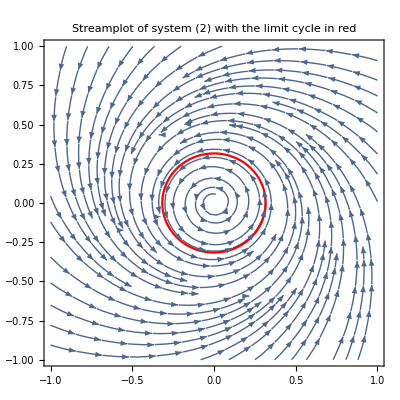

```mathematica
p1 = StreamPlot[
{x/10 - y^3 - x*y^2-x^2y-y-x^3,
x+ y/10+x*y^2+ x^3- y^3- x^2y
},
{x, -1,1},
{y,-1,1}
];
mu0 = 1/10;
w0 = 1;
v0 = 1;
x0 = Sqrt[mu0];
tMax = 2*Pi/(w0+mu0*v0);

sol = NDSolve[
{x'[t] ==x[t]/10 - y[t]^3 - x[t]y[t]^2-x[t]^2y[t]- y[t] -x[t]^3,
y'[t] == x[t]+ y[t]/10+x[t]y[t]^2+ x[t]^3- y[t]^3- x[t]^2y[t],
x[0] == x0,
y[0] == 0
}, 
{x[t],y[t]}, 
{t, 0, tMax}
];

p2 = ParametricPlot[Evaluate[{x[t], y[t]}/.sol], 
{t, 0, tMax},
PlotStyle->{RGBColor[1,0,0]}
];
title = "Streamplot of system (2) with the limit cycle in red";
Show[p1,p2, PlotLabel->Style[title,FontSize->15]]
```

```mathematica
TransformedField["Polar" -> "Cartesian", Cos*(mu*r-r^3) - r*Sin*(w+v*r^2), {r,t}->{x,y}]

TransformedField["Polar" -> "Cartesian", Sin*(mu*r-r^3) + r*Cos*(w+v*r^2), {r,t}->{x,y}]
```

mu x-x^3-w y-v x^2 y-x y^2-v y^3

w x+v x^3+mu y-x^2 y+v x y^2-y^3